坐标与图形

我们已经用过 ListPlot 和 ListLinePlot 来绘制数值的列表，其中每个数值都出现在前一个数值之后。但如果给出包含坐标对的列表，而不是单个数值，我们可以使用这些函数在任意位置绘制点。

绘制数值列表，每个数值都出现在前一个数值之后：

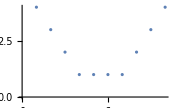

```mathematica
ListPlot[{4,3,2,1,1,1,1,2,3,4}]
```

绘制一系列由 {x, y} 坐标指定的任意点：

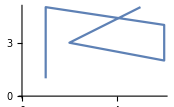

```mathematica
ListLinePlot[{{1,1},{1,5},{6,4},{6,2},{2,3},{5,5}}]
```

这里每个点的位置是由 {x, y} 坐标指定的。按照数学的标准惯例，x 值表示该点在水平方向上应该有多远；y 值表示它在竖直方向上应该有多远。

生成一系列随机的 {x, y} 坐标：

```mathematica
Table[RandomInteger[20],10,2]
```

{{19,8},{11,20},{14,15},{5,8},{6,4},{16,14},{1,17},{10,7},{5,6},{17,2}}

另一种获取随机坐标的方法：

```mathematica
RandomInteger[20,{10,2}]
```

{{2,2},{20,18},{16,2},{13,13},{6,15},{11,18},{10,20},{17,20},{8,14},{2,10}}

绘制 100 个随机坐标点：

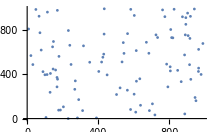

```mathematica
ListPlot[Table[RandomInteger[1000],100,2]]
```

我们可以使用坐标来构建图形。之前我们已经看过如何创建一个圆的图形。要创建多个圆的图形，我们就必须说明每个圆的位置，可以通过给出它们的中心坐标来做到这一点。

通过给出圆心的坐标来放置圆：

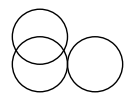

```mathematica
Graphics[{Circle[{1,1}],Circle[{1,2}],Circle[{3,1}]}]
```

如果我们应用颜色样式，就能更容易地看出哪个圆是哪个圆：

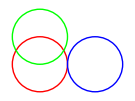

```mathematica
Graphics[{Style[Circle[{1,1}],Red],Style[Circle[{1,2}],Green],Style[Circle[{3,1}],Blue]}]
```

创建包含 100 个随机放置的圆的图形，每个圆的中心坐标最大为 50：

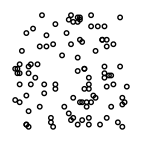

```mathematica
Graphics[Table[Circle[RandomInteger[50,2]],100]]
```

一个由圆组成的二维数组，其排列方式是使它们刚好接触：

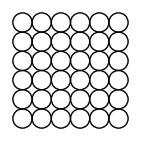

```mathematica
Graphics[Table[Circle[{x,y}],{x,0,10,2},{y,0,10,2}]]
```

Circle[{x,y}] 表示以位置 {x,y} 为中心的圆。如果你不指定，这个圆的半径将是 1。你可以用 Circle[{x,y},r] 来创建一个任意半径的圆。

使用不同的半径来创建不同的圆：

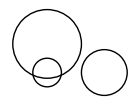

```mathematica
Graphics[{Circle[{1,1},0.5],Circle[{1,2},1.2],Circle[{3,1},0.8]}]
```

创建 10 个同心圆：

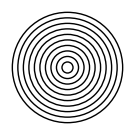

```mathematica
Graphics[Table[Circle[{0,0},r],{r,10}]]
```

画出中心逐渐向右移动，半径逐渐变大的一系列圆：

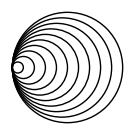

```mathematica
Graphics[Table[Circle[{x,0},x],{x,10}]]
```

绘制位置和半径都为随机值的圆：

```mathematica
Graphics[Table[Circle[RandomInteger[50,2],RandomInteger[10]],100]]
```

-Graphics-

RegularPolygon 的工作原理与 Circle 和 Disk 基本相同，只是除了给出中心位置和大小之外，你还必须指定多边形应该有多少条边。

创建一个大小为 1 的正五边形和一个大小为 0.5 的正七边形的图形：

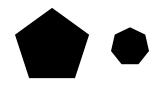

```mathematica
Graphics[{RegularPolygon[{1,1},1,5],RegularPolygon[{3,1},0.5,7]}]
```

你可以将不同类型的图形对象混合起来：

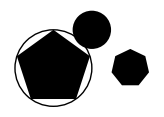

```mathematica
Graphics[{RegularPolygon[{1,1},1,5],Circle[{1,1},1],RegularPolygon[{3,1},.5,7],Disk[{2,2},.5]}]
```

要创建任意的图形，你需要基本的图形基元，点(Point)、线(Line)以及多边形(Polygon)。Point[{x,y}] 表示在坐标位于 {x,y} 的一个点。为了获取多个点，你可以给出一个 Point[{x,y}] 列表，也可以在一个 Point 内给出一个坐标位置列表。

在指定位置的三个点的图形：

```mathematica
Graphics[{Point[{0,0}],Point[{2,0}],Point[{1,1.5}]}]
```

-Graphics-

另一种形式，所有的坐标位置都被放置在一个列表中：

```mathematica
Graphics[Point[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

创建线段来将这些位置连接起来：

```mathematica
Graphics[Line[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

创建一个多边形，角点在你给的位置上：

```mathematica
Graphics[Polygon[{{0,0},{2,0},{1,1.5}}]]
```

-Graphics-

RegularPolygon 用于创建正多边形，其中所有的边和角都是一样的。Polygon 让你可以创建任意多边形，甚至是自身相重叠的奇怪的东西。

一个包含 20 个角的多边形，角点为 100 以内的随机数值；该多边形自身相重叠：

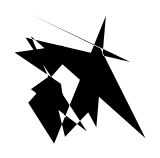

```mathematica
Graphics[Polygon[Table[RandomInteger[100],20,2]]]
```

到目前为止，我们在这里所做的事情都可以立刻推广到三维。我们不再使用两个坐标 {x, y}，而是使用三个：{x, y, z}。在 Wolfram 语言中，x 默认为横跨屏幕的方向，y 为“穿过”屏幕的方向，而 z 为延伸到屏幕上方的方向。

两个球体相互堆叠在一起：

```mathematica
Graphics3D[{Sphere[{0,0,0}],Sphere[{0,0,2}]}]
```

-Graphics3D-

一个球体的三维数组，半径为 1/2 使它们刚好互相接触：

```mathematica
Graphics3D[Table[Sphere[{x,y,z},1/2],{x,5},{y,5},{z,5}]]
```

-Graphics3D-

三维点数组：

```mathematica
Graphics3D[Table[Point[{x,y,z}],{x,10},{y,10},{z,10}]]
```

-Graphics3D-

50 个球处于随机的三维位置，每个坐标最大值不超过 10：

```mathematica
Graphics3D[Table[Sphere[RandomInteger[10,3]],50]]
```

-Graphics3D-

如果你不指定，像球体这样的三维物体默认是实心的，所以你不能看穿它们。但是，就像你可以指定某个对象是什么颜色一样，你也可以指定它的不透明度。不透明度为 1 意味着完全不透明，所以你根本无法看透它；不透明度为0 则意味着完全透明。

为所有球体指定不透明度为 0.5：

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],Opacity[0.5]],50]]
```

-Graphics3D-

你可以使用 Manipulate 来创建可以交互操作的 2D 或 3D 图形。

操作第二个球体的位置和不透明度：

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0}],Style[Sphere[{x,0,0}],Opacity[o]]}],{x,1,3},{o,0.5,1}]
```

词汇

Point[{x,y}] |   | 位于坐标 {x,y} 处的点
Line[{{1,1},{2,4},{1,2}}] |   | 将指定坐标进行连接的线
Circle[{x,y}] |   | 圆心位于 {x,y} 处的圆
Circle[{x,y},r] |   | 圆心位于 {x,y} 并且半径为 r 的圆
RegularPolygon[{x,y},s,n] |   | 中心位于 {x,y} 边长为 s 的正 n 边形
Polygon[{{1,1},{2,4},{1,2}}] |   | 角点位于指定位置的多边形
Sphere[{x,y,z}] |   | 中心位于 {x,y,z} 处的球
Sphere[{x,y,z},r] |   | 中心位于 {x,y,z} 并且半径为 r 的球
Opacity[level] |   | 指定不透明度级别(0：透明；1：不透明)

"共有 10 道习题"
"以及 6 道附加题" | "开始练习 »"

创建位于 {0,0} 处的五个同心圆的图像，半径分别为 1、2 ... 5。»

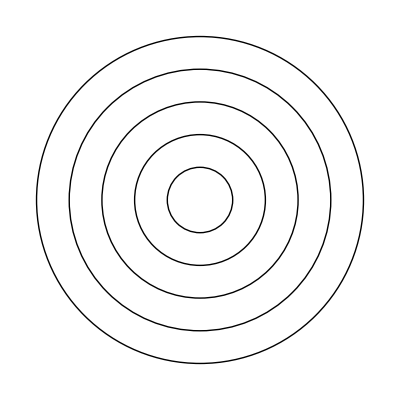
| 期望输出： |  
  | -Graphics- |

创建 10 个颜色随机的同心圆，半径分别为 1、2 ... 10。»

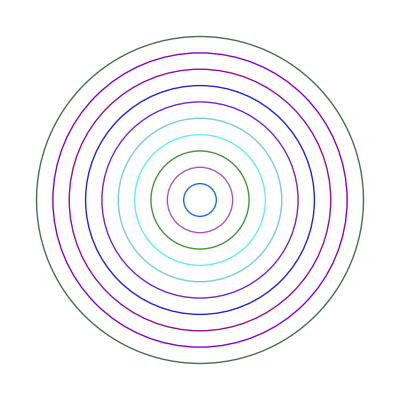
| 期望输出示例： |  
  | -Graphics- |

创建中心位于整数点 {x,y} 处，半径为 1 的 10×10 的圆的图形。»

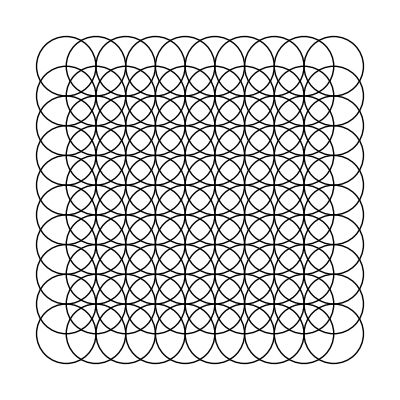
| 期望输出： |  
  | -Graphics- |

创建一个 10×10 的网格点，坐标为 10 以内的整数。»

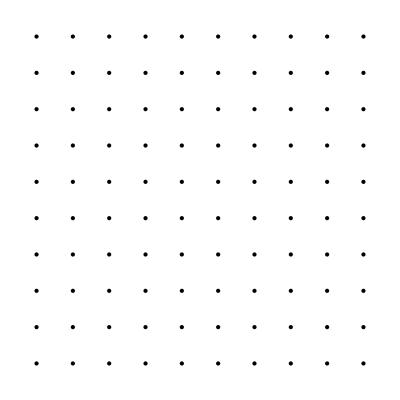
| 期望输出： |  
  | -Graphics- |

创建一个操作界面，显示 1 到 20 个同心圆。»

| 期望输出： |  
  |  |

放置 50 个随机颜色的球，球的中心位于 10 以内的随机整数坐标上。»

| 期望输出示例： |  
  | -Graphics3D- |

创建一个 10×10×10 的球的数组，球的中心坐标为整数，RGB 分量随着中心坐标从 0 变化到 1。并且要互相接触。»

| 期望输出： |  
  | -Graphics3D- |

创建一个操作界面，使得 t 可以在 -2 到 +2 之间变化，绘制以 {t*x,0} 为中心，半径为 x 的圆，x 从 1 变化 10。»

| 期望输出： |  
  |  |

创建一个 5×5 的正六边形数组，大小为 1/2，以整数点为中心。»

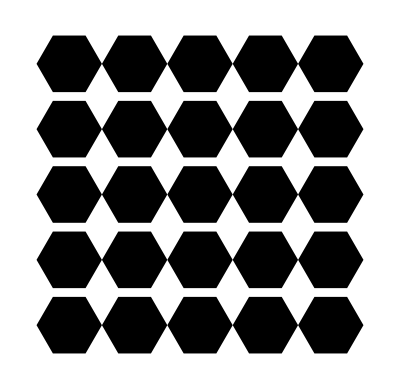
| 期望输出： |  
  | -Graphics- |

在 3D 空间中创建一条穿过 50 个随机点的线，这些点的坐标为 50 以内的随机整数。»

| 期望输出示例： |  
  | -Graphics3D- |

创建一个操作界面，来绘制一个 n×n 的网格点，n 可以从 5 到 20 之间变化。»

| 期望输出： |  
  |  |

放置 30 个半径为 1，中心坐标为 10 以内的随机整数、颜色随机的圆。»

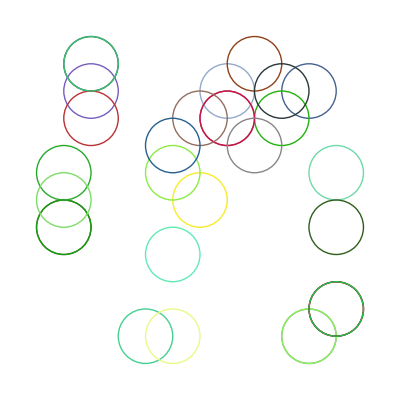
| 期望输出： |  
  | -Graphics- |

显示 100 个边长为 10、不透明度为 0.5、颜色随机、边数为 3 到 8 的随机整数、中心为 100 以内的随机整数的多边形。»

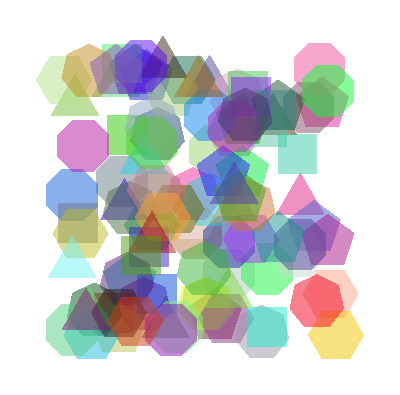
| 期望输出： |  
  | -Graphics- |

创建一个 10×10×10 的三维点阵列，每个点的颜色随机。»

| 期望输出： |  
  | -Graphics3D- |

取 10 到 100 的数字的前两位数，画一条以它们为坐标的线。»

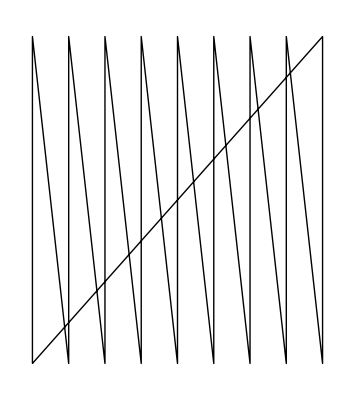
| 期望输出： |  
  | -Graphics- |

取 100 到 1000 的数字的前三位数，在三维空间中画一条以它们为坐标的线。»

| 期望输出： |  
  | -Graphics3D- |

问&答

什么决定了所显示的坐标范围？

默认情况下，它是自动选择的，但你可以使用 PlotRange 选项明确地设置它，将在第 20 节中进行讨论。

如何将轴放在图形上？

使用选项 Axes→True(详见第 20 节)。

如何改变多边形或圆盘的边缘的外观？

在 Style 内使用 EdgeForm。

还有哪些图形结构？

还有很多。包括 Text(用于在图形内放置文本)、Arrow(用于在线条等对象上放置箭头)、Inset(用于在图形内放置图形)以及 FilledCurve。

如何去除 3D 图形周围的方框？

使用选项 Boxed→False(详见第 20 节)。

技术笔记

这里的随机圆圈是绘制在整数坐标上的。你可以使用 RandomReal 来把它们放到任意坐标上。

你可以在一个列表中为图形给出指令，而不是使用 Style，比如 {Red,Disk[ ]}。一个特定的指令将影响在列表中出现在它后面的每一个图形对象。

在二维图形中，物体是按照你给出它们的顺序来绘制的，所以后面的物体会遮盖先前的物体。

你可以使用像 Translate、Scale 以及 Rotate 这些函数来对图形对象进行几何变换。

自身重叠的多边形(例如，创建领结形状)将使用偶-奇规则来显示。

三维图形可以包括 Cuboid、Tetrahedron 以及由 PolyhedronData 指定多面体，还有由三维空间中的任意网格点定义的形状。

探索更多

Wolfram 语言中的图形指南 »